```mathematica
(* Time constants *)
```

```mathematica
taumRNA=25;
TRim4 =20;
invtauRim4=0.2;
```

```mathematica
(* Rim4-mRNA dissociation curve *)
```

```mathematica
Rim4[t_]:=(1-Tanh[invtauRim4(t-TRim4)])/2;
```

```mathematica
(* Protein numbers to concentration (in a.u.) conversion *)
```

```mathematica
V=10 10^(-12); 
NA = 6.023 10^23;
vna = V NA (100 10^(-9)) 10^(-3);
ivna = 1/vna;
```

```mathematica
(* Clb4 *)
```

```mathematica
kClb4s=0.0008;
kClb4sp=0.009;
kClb4d=0.02;
kClb4dp=0.2;
kClb4dpp=0.02;
kClb1Cdc20d=0.2;
```

```mathematica
(* Clb1 *)
```

```mathematica
kClb1s=0.04;
kClb1sp=0.024;
kClb1d=0.1;
kClb1dp=0.5;
kClb1dpp=0.02;
kClb1Cdc20d=0.8;
```

```mathematica
(* Clb3 *)
```

```mathematica
kClb3s=0.002;
kClb3sp=0.000114;
kClb3d=0.34;
kClb3dp = 0.2;
kClb3dpp=0.02;
kClb3Cdc20d=0.4;
alphaClb3=0.4/kClb3sp;
```

```mathematica
(*  Cdc5 *)
```

```mathematica
kCdc5s=0.004;kCdc5sp=0.027;kCdc5d=0.04;kCdc5dp=0.003;kCdc5dpp=0.002;kCdc5a=0.1;kCdc5ap=1.2;kCdc5app=1.2;
kCdc5appp=2;kCdc5i=2;
```

```mathematica
(* Ndt80 *)
```

```mathematica
kNdt80s=0.01;
kNdt80sp=2;
kNdt80d=0.093;
kNdt80dp=0.013;
nHill=1.62;
KHill=10.52;
```

```mathematica
(* Ama1 *)
```

```mathematica
kAma1a=0.1;
kAma1i=0.005;
kAma1ip=0.5;
JAma1=0.1;
JAma1p=0.1;
kAma1d=0.02;
kAma1dp=0.02;
kAma1s=0.04;
alphaAma1 = 0.4/kAma1s;
```

```mathematica
(* APC/C-Cdc20 *)
```

```mathematica
kAPCPCdc20a =0.25;
JAPCPCdc20a=0.1;
kAPCPCdc20d = 0.32;
JAPCPCdc20d = 0.1;
```

```mathematica
(* APC/C *)
```

```mathematica
kAPCClb1p=0.09;
JAPCClb1 = 0.001;
kAPCClb4p=0.09;
JAPCClb4 = 0.001;
kAPCClb3p=0.09;
JAPCClb3=0.001;
kAPCdp=0.072;
JAPCP=0.01;
APCtot = 5 vna;
```

```mathematica
(* Cdc20 *)
```

```mathematica
kCdc20s=0.1; 
kCdc20sp = 0.001;
kCdc20d=0.05; 
kCdc20dp=0.02;
```

```mathematica
(* Use NDSolveValue[] with StiffnessSwitching *)
```

```mathematica
{Clb1Nv7,  Clb4Nv7,Ndt80Nv7, Ama1PNv7, Ama1Nv7, APCpNv7, APCpCdc20Nv7,Cdc20TNv7,Clb3Nv7,Cdc5TNv7, Cdc5ANv7}= NDSolveValue[

{Clb1'[t]== 1.0(kClb1s*vna + kClb1sp * Ndt80[t] - (kClb1d +  kClb1dp*ivna * Ama1[t]+ kClb1dpp*ivna * (Ama1[t]+Ama1P[t])+kClb1Cdc20d*ivna*APCpCdc20[t]) * Clb1[t]),

Clb4'[t]== 1.0(kClb4s*vna +  kClb4sp * Ndt80[t] - (kClb4d +  kClb4dp*ivna * Ama1[t]+ kClb4dpp*ivna * (Ama1[t]+Ama1P[t])+ kClb4Cdc20d*ivna*APCpCdc20[t]) * Clb4[t]),

Clb3'[t]==1.0(kClb3s*vna - (kClb3d + kClb3dp*ivna * Ama1[t]+ kClb3dpp*ivna * (Ama1[t]+Ama1P[t])+ kClb3Cdc20d*ivna*APCpCdc20[t])* Clb3[t]+kClb3sp(1-Rim4[t])* Ndt80[t]+alphaClb3*kClb3sp*vna*(1-Rim4[t])*Exp[-(t-TRim4)/taumRNA]),


Ndt80'[t]==1.0(kNdt80s*vna+kNdt80sp*vna*((Ndt80[t]/vna)^nHill)/(((Ndt80[t]/vna)^nHill)+KHill^nHill)- kNdt80d * Ndt80[t]-kNdt80dp*ivna*Ama1[t]* Ndt80[t]),


Cdc20T'[t]== 1.0(kCdc20s*vna+ kCdc20sp * Ndt80[t] -kCdc20d*Cdc20T[t]-kCdc20dp APCpCdc20[t]),


APCp'[t]==kAPCClb4p* Clb4[t] * (APCtot - APCp[t]-APCpCdc20[t])/(JAPCClb4*vna+(APCtot - APCp[t]-APCpCdc20[t]))+kAPCClb1p Clb1[t] * (APCtot - APCp[t]-APCpCdc20[t])/(JAPCClb1*vna+(APCtot - APCp[t]-APCpCdc20[t]))+  
kAPCClb3p Clb3[t] * (APCtot - APCp[t]-APCpCdc20[t])/(JAPCClb3*vna+(APCtot - APCp[t]-APCpCdc20[t]))
-kAPCdp* vna*APCp[t]/(JAPCP*vna+APCp[t]),


APCpCdc20'[t]== kAPCPCdc20a APCp[t] (Cdc20T[t]-APCpCdc20[t])/(JAPCPCdc20a*vna +Cdc20T[t]-APCpCdc20[t]) - kAPCPCdc20d *vna*APCpCdc20[t]/(JAPCPCdc20d*vna + APCpCdc20[t]),

Ama1P'[t]==1.0 ((kAma1i+kAma1ip*ivna*Clb1[t]) * Ama1[t]*vna/(JAma1*vna+Ama1[t])-kAma1a * Ama1P[t]*vna/(JAma1p*vna+Ama1P[t])-kAma1dp*Ama1P[t] +kAma1ip*ivna*Clb3[t] * Ama1[t]*vna/(JAma1*vna+Ama1[t])+kAma1ip*ivna*Clb4[t] * Ama1[t]*vna/(JAma1*vna+Ama1[t])),

Ama1'[t]==1.0 (kAma1s*vna-kAma1dp*Ama1[t]+ kAma1a * Ama1P[t]*vna/(JAma1p*vna+Ama1P[t])-(kAma1i+ kAma1ip*ivna*Clb1[t]) * Ama1[t]*vna/(JAma1*vna+Ama1[t])-kAma1ip*ivna*Clb4[t] * Ama1[t]*vna/(JAma1*vna+Ama1[t])- kAma1ip*ivna*Clb3[t] * Ama1[t]*vna/(JAma1*vna+Ama1[t])+alphaAma1*kAma1s*vna*(1-Rim4[t])*Exp[-(t-TRim4)/taumRNA] ),

Cdc5T'[t]== 1.0(kCdc5s*vna +kCdc5sp * Ndt80[t] - (kCdc5d + kCdc5dp * ivna*Ama1[t]+kCdc5dpp * ivna*(Ama1[t]+Ama1P[t])) * Cdc5T[t]),

Cdc5A'[t]== 1.0((kCdc5a + kCdc5ap *ivna* Clb1[t]+ kCdc5app *ivna* Clb4[t]+ kCdc5app *ivna* Clb3[t])*(Cdc5T[t] - Cdc5A[t])-kCdc5i*Cdc5A[t]-(kCdc5d +kCdc5dp* ivna*Ama1[t]+ kCdc5dpp* ivna*(Ama1[t]+Ama1P[t]) ) * Cdc5A[t]),

Clb1[0]== 1.125 vna,
Clb4[0]==0.12 vna,
Ndt80[0]==5 vna,
Ama1P[0]==0 vna,
Ama1[0]==0 vna,
APCp[0]==0 vna,
APCpCdc20[0]== 0.1 vna,
Cdc20T[0]==2vna,
Clb3[0]==0,
Cdc5T[0]==  0.75vna,
Cdc5A[0]== 0.25 vna},

{Clb1,Clb4,Ndt80, Ama1P, Ama1,APCp,APCpCdc20,Cdc20T,Clb3, Cdc5T, Cdc5A},{t, 10000}, Method->{ "TimeIntegration"->{"StiffnessSwitching"} },  AccuracyGoal->10, PrecisionGoal->10, MaxSteps->Infinity ]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
(* Full model dynamics *)
```

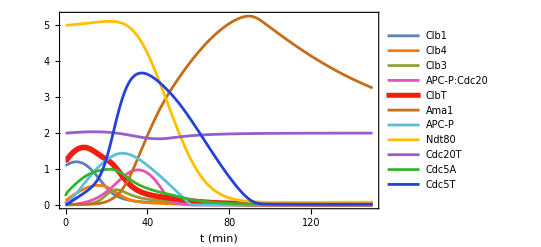

```mathematica
Plot[{Clb1Nv7[t]/vna,  Clb4Nv7[t]/vna, Clb3Nv7[t]/vna,APCpCdc20Nv7[t]/vna, Clb1Nv7[t]/vna+  Clb3Nv7[t]/vna+Clb4Nv7[t]/vna,  Ama1Nv7[t]/vna,APCpNv7[t]/vna,Ndt80Nv7[t]/vna,Cdc20TNv7[t]/vna,Cdc5ANv7[t]/vna,Ama1PNv7[t]/vna},{t,0,150}, PlotRange->{{0,150}, All}, PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[1, 0.48, 0],RGBColor[0.560181, 0.63, 0.194885],RGBColor[0.922526, 0.31, 0.72],{Thickness[0.01],Hue[0.01, 0.93, 0.9400000000000001]},RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.75, 0.84],RGBColor[1, 0.75, 0],RGBColor[0.59, 0.36, 0.8200000000000001],RGBColor[0.2, 0.715, 0.16],RGBColor[0.14, 0.26, 0.85],RGBColor[0.18, 0.41000000000000003, 0.]},PlotLegends->{"Clb1", "Clb4", "Clb3","APC-P:Cdc20", "ClbT","Ama1", "APC-P", "Ndt80","Cdc20T", "Cdc5A", "Cdc5T","Ama1-P"}, LabelStyle->Directive[FontFamily->"Arial",FontSize->22], FrameLabel->{"t (min)"}, FrameStyle->Thick,PlotStyle->{Thickness[0.0075]},Frame->True]
```